# Vaje 6

3. 4. 2025

## 1. Naloga

a) Dana je funkcija . Definirajte funkcijo dveh spremenljivk.

```mathematica
f[x_,y_]:=x^3+y^3-3x*y;
```

b) Izračunajte gradient funkcije (par, kjer je na prvem mestu odvod funkcije po x in na drugem mestu odvod funkcije po y). Kdaj je gradient enak 0?

```mathematica
gradient = {D[f[x,y],x], D[f[x,y], y]}
```

{3 x^2-3 y,-3 x+3 y^2}

```mathematica
gradient1 = Grad[f[x,y],{x,y}]
```

{3 x^2-3 y,-3 x+3 y^2}

```mathematica
kriticneTocke = Solve[gradient==0, Reals]
```

{{x→0,y→0},{x→1,y→1}}

c) Definirajte Hessejevo matriko za funkcijo  in ugotovite, ali je v točki, kjer je gradient funkcije enak 0, dosežen lokalni ekstrem.

```mathematica
(* Funkcije dveh spremenljivk imam maksimum v točki x0, y0 natanko tedaj,
 kadaj je determinanta Hessejeve matrike > 0 in f_xx (drugi odvod po x) je negativen *)

(* Funkcije dveh spremenljivk imam minimum v točki x0, y0 natanko tedaj, 
kadaj je determinanta Hessejeve matrike > 0 in f_xx (drugi odvod po x) je pozitiven *)

(* Če je determinanta < 0, potem je v točki x0, y0 sedlo *)
(* Če je determinanta enaka 0, ne vemo ničesar *)
```

```mathematica
Hesse = {
{D[f[x,y],{x,2}],D[f[x,y],{x},{y}]},
{D[f[x,y],{y},{x}],D[f[x,y],{y,2}]}
} // MatrixForm
```

(6 x | -3
-3 | 6 y)

```mathematica
HesseVTocki1 = Hesse /. kriticneTocke[[1]] (* v točki 0, 0 imamo lokalni maksimum*)
```

(0 | -3
-3 | 0)

```mathematica
%//Det
```

-9

```mathematica
HesseVTocki2 = Hesse /. kriticneTocke[[2]] (* v točki 1, 1 imamo lokalni minimum*)
```

(6 | -3
-3 | 6)

d) Narišite nivojnico  in označite kritične točke. Vrednost paramtera  naj bo moč spreminjati. Narišite tudi graf funkcije f in označite lokalni minimum.

```mathematica
Manipulate[
ContourPlot[
f[x,y] == a, {x, -2,2}, {y,-2,2},
ContourStyle->Red,
Epilog->{Blue, PointSize[Large],Point[{x,y}/.kriticneTocke[[1]]],
Orange,PointSize[Large],Point[{x,y}/.kriticneTocke[[2]]]}
],
{a,-5,5}
]
```

Show::gcomb: Could not combine the graphics objects in ….

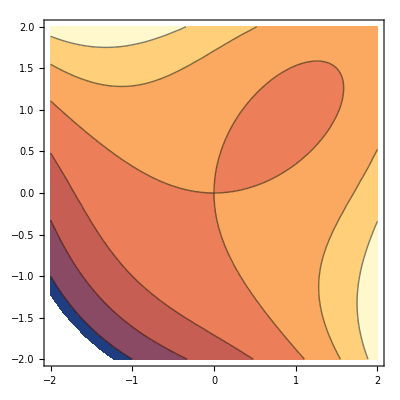
Show[-Graphics3D-,-Graphics-,-Graphics3D-]

```mathematica
Show[Plot3D[f[x,y], {x,-2,2}, {y,-2,2}],
ContourPlot[f[x,y], {x,-2,2}, {y,-2,2}],
Graphics3D[{Blue,PointSize[Large],Ball[{1,1,f[1,1]},0.1]}]
]
```

## 2. Naloga

Dana je enačba ploskve .

```mathematica
ploskev = {x^2+y^2-z^3==1}
```

{x^2+y^2-z^3==1}

a) Poiščite precečišča te ploskve s koordinatnimi ravninami.

b) Narišite ploskev v 3D.

## 3. Naloga

Dana je funkcija .

```mathematica
f[x_]:=E^x*Cos[x^3]
```

a) Razvijte funkcijo v Taylorjev polinom stopnje 6 okoli točke 0.

```mathematica
polinom=Normal[Series[f[x],{x,0,6}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120-(359 x^6)/720

b) Narišite originalno funkcijo in njeno aproksimacijo na intervalu [-2, 2].

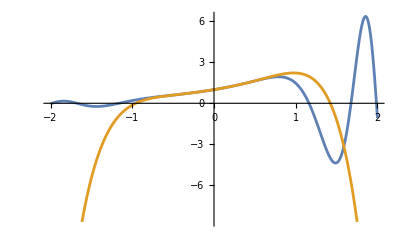

```mathematica
Plot[{f[x],polinom},{x,-2,2}]
```

## 4. Naloga

a) Aproksimiraj  s Taylorjevim polinomom stopnje 2 okoli x=0 in oceni napako.

```mathematica
ClearAll[priblizek]
priblizek[t_] := Normal[Series[Cos[x],{x,0,2}]]/.x->t
```

```mathematica
pribliznaVrednost = priblizek[0.1]
```

0.995

```mathematica
razlika = Cos[0.1] - pribliznaVrednost
```

4.16528×10^-6

b) Uporabi Taylorjev polinom stopnje 3 za izračun približka .

```mathematica
priblizek[t_]:=Normal[Series[Log[x],{x,1,2}]]/. x ->t
pribliznaVrednost = priblizek[1.1]
dejanskaVrednost = Log[1.1]
```

0.095

0.0953102

```mathematica
dejanskaVrednost - pribliznaVrednost
```

0.00031018

## 5. Naloga

a) Poišči radij konvergence Tylorjeve vrste  okoli .

```mathematica
f[x_]=Divide[1,1+x^2]
```

1/(1+x^2)

```mathematica
f[0]
```

1

b) Določij konvergenčni polmer vrste .